{7,8} | {16,2} | {12,13} | {8,9} | {9,10}
{11,8} | {6,2} | {2,13} | {5,9} | {3,10}

( | 1 | 2 | 3 | 4 | 5 | 6 | 7 | 8 | 9 | 10 | 11 | 12 | 13 | 14 | 15 | 16
1 | 1 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
2 | 1 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0
3 | 0 | 0 | 1 | 1 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
4 | 0 | 0 | 0 | 1 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
5 | 0 | 0 | 0 | 0 | 1 | 1 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
6 | 0 | 1 | 0 | 0 | 0 | 1 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
7 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
8 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
9 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
10 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 1 | 0 | 0 | 0 | 0 | 0
11 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 1 | 1 | 0 | 0 | 0 | 0
12 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
13 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 1 | 0 | 0
14 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 1 | 0
15 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 1
16 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1)

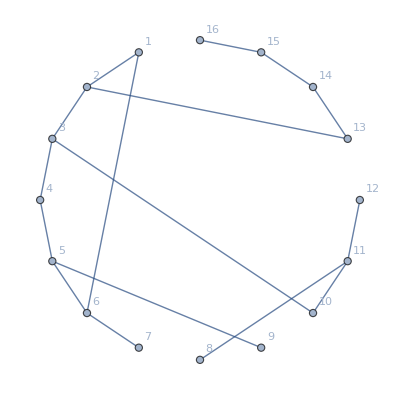

451/120

```mathematica
ClearAll["Global`*"]
(*----------2 Rewireing Networks----------*)
(*----------Basic Setup----------*)
n=16;
r=5;


(*----------Distance Matrice between the nodes----------*)
m=IncidenceMatrix[CycleGraph[n]];
(*---m[[2,3]]=0; m[[7,3]]=1;---*)
(*----------Rewireing----------*)
(*-----m[[coloumn,row]]-----*)
outputString={{(*old*)},{(*new*)}};
Do[
mjEdge=Random[Integer,{1,n}];
For[j=1,j<n+1,j++,
If[m[[j,mjEdge]]==1 && j≠mjEdge ,
miOld=j;
];
];
Label[againRandom];
miNew=Random[Integer,{1,n}];
If[miNew == mjEdge || miNew==miOld,Goto[againRandom],Goto[check]];
Label[check];
AppendTo[outputString[[1]],{miOld,mjEdge}];
AppendTo[outputString[[2]],{miNew,mjEdge}];
m[[miOld,mjEdge]]=0;
m[[miNew,mjEdge]]=1;
,r];

(*----------------------------*)
Grid[outputString,Frame->{All,None}]


matrixLabel=Table[x,{x,n}];
MatrixForm[m, TableHeadings->{matrixLabel,matrixLabel}]

IncidenceGraph[m,VertexLabels->"Name",EdgeLabels->"Name"];
m=IncidenceGraph[m];
Table[Graph[m,GraphLayout->l,VertexLabels->Automatic],{l,{"CircularEmbedding"}}]

(*----------Average Path Length Calculation----------*)


(*----------Output----------*)
MeanGraphDistance[m]
```